# Лабораторная работа №3.4.2 Закон Кюри - Вейсса

Цель работы :
Изучение температурных зависимостей магнитной восприимчивости ферромагнетизм выше точки Кюри.

В работе используются:
Катушка самоиндукции из гадолиния, термостат, частотомер, цифровой вольтметр, LC - автогенератор, термопара медь - константан.

Теоретические основы:
Вещества с отличными от нуля атомными магнитными моментами обладают парамагнитными свойствами. Внешнее магнитное поле ориентирует магнитные моменты, которые в отсутствие поля располагались в пространстве хаотичным образом.
При повышении температуры   возрастает дезориентирующее действие теплового движения частиц, и магнитная восприимчивость парамагнетиков убывает, в простейшем случае (в постоянном магнитном поле – по закону Кюри:

```mathematica
χ==c/T
```

где с  – постоянная Кюри.
Для парамагнитных веществ, которые при понижении температуры становятся ферромагнитными, формула [1] должна быть видоизменена. Эта формула показывает, что температура   является особой точкой температурной кривой, в которой   неограниченно возрастает.
При T → 0 тепловое движение всё меньше препятствует магнитным моментам атомов ориентироваться в одном направлении при сколь угодно слабом внешнем поле. В ферромагнетиках – под влиянием обменных сил – это происходит при понижении температуры не до абсолютного нуля, а до температуры Кюри Θ. Оказывается, что у ферромагнетиков закон Кюри должен быть заменен законом Кюри - Вейсса:

```mathematica
χ∼1/(T-Subscript[Θ, p])
```

где Θ_p – температура, близкая к температуре Кюри.
Эта формула хорошо описывает поведение ферромагнитных веществ после их перехода в парамагнитную фазу при заметном удалении температуры от Θ , но недостаточно точна при T ≈ Θ.
Иногда для уточнения формулы (2) вводят вместо одной две температуры Кюри, одна из которых описывает точку фазового перехода – ферромагнитная точка Кюри Θ, а другая является параметром в формуле (2) – парамагнитная точка Кюри Θ_p(рис. 1).

```mathematica
-Graphics-
Рис. 1. Зависимость обратной величины магнитной восприимчивости от температуры.
```

В нашей работе изучается температурная зависимость χ(T) гадолиния при температурах выше точки Кюри. Выбор материала определяется тем, что его точка Кюри лежит в интервале комнатных температур.
Экспериментальная установка.
Схема установки для проверки закона Кюри - Вейсса показана на рис. 2. Исследуемый ферромагнитный образец (гадолиний) расположен внутри пустотелой катушки самоиндукции, которая служит индуктивностью колебательного контура, входящего в состав LC-автогенератора. Автогенератор собран на полевом транзисторе КП-103 и смонтирован в виде отдельного блока.

```mathematica
-Graphics-
Рис. 2. Схема экспериментальной установки.
```

Гадолиний является хорошим проводником электрического тока, а рабочая частота генератора достаточно велика (~50 кГц), поэтому для уменьшения вихревых токов образец изготовлен из мелких кусочков размером около 0,5 мм. Катушка 1 с образцом помещена в стеклянный сосуд 2, залитый трансформаторным маслом. Масло предохраняет образец от окисления и способствует ухудшению электрического контакта между отдельными частичками образца. Кроме того, оно улучшает тепловой контакт между образцом и термостатируемой (рабочей) жидкостью 3 в термостате. Ртутный термометр 4 используется для приближенной оценки температуры. Температура образца регулируется с помощью термостата.
Магнитная восприимчивость образца   определяется по изменению самоиндукции катушки. Обозначив через   самоиндукцию катушки с образцом и через   – её самоиндукцию в отсутствие образца, получим:

```mathematica
(L-Subscript[L, 0])~χ
```

При изменении самоиндукции образца меняется период колебаний автогенератора:

```mathematica
τ=2π √(L c)
```

где c – ёмкость контура автогенератора.
Период колебаний в отсутствие образца определяется самоиндукцией пустой катушки:

```mathematica
Subscript[τ, 0]=2π √(Subscript[L, 0] c)
```

Отсюда имеем:

```mathematica
(L-Subscript[L, 0])~(τ^2-Subscript[τ, 0]^2)
```

Таким образом,

```mathematica
χ~(τ^2-Subscript[τ, 0]^2)
```

Из формул (2) и (6) следует, что закон Кюри - Вейсса справедлив, если выполнено соотношение:

```mathematica
1/χ~(T-Subscript[Θ, p])~1/(τ^2-Subscript[τ, 0]^2)
```

Измерения проводятся в интервале температур от 14°C до 40°C. С целью экономии времени следует начинать измерения с низких температур.
Для охлаждения образца используется холодная водопроводная вода, циркулирующая вокруг сосуда с рабочей жидкостью (дистиллированной водой); рабочая жидкость постоянно перемешивается.
Величина стабилизирующей температуры задается на дисплее 5 термостата. Для нагрева служит внутренний электронагреватель, не показанный на рисунке. Когда температура рабочей жидкости в сосуде приближается к заданной, непрерывный режим работы нагревателя автоматически переходит в импульсный – начинается процесс стабилизации температуры.
Температура исследуемого образца всегда несколько отличается от температуры дистиллированной воды в сосуде. После того, как вода достигла заданной температуры, идёт медленный процесс выравнивания температур образца и воды. Разность их температур контролируется с помощью медно-константановой термопары 6 и цифрового вольтметра. Один из спаев термопары находится в тепловом контакте с образцом, а другой погружён в воду. Концы термопары подключены к цифровому вольтметру.
Задание
	1.	Подготовим приборы к работе.
	2.	Оценим допустимую ЭДС термопары, если допустимая разность температур образца и рабочей жидкости ΔT = 0,5 °С, а постоянная термопары k = 24 град/мВ.

ΔU=0.5/24=2.08333×10^-2 мВ/с≈21 мкВ/с

3.	Исследуем зависимость периода колебаний LC-генератора от температуры образца, отмечая период колебаний τ по частотомеру, а температуру T – по показаниям дисплея и цифровому вольтметру (ΔU с учетом знака). Термопара подключена так, что при знаке «+» на табло вольтметра температура образца выше температуры рабочей жидкости.

```mathematica
ClearAll[Experiment]
Experiment={{"T,°C", "∆U, мВ", "t, мкс"}, {12.73, 0.002, 10.8325}, {14, -0.014, 10.80460}, {16.10, -0.001, 10.66180}, {17.99, -0.005, 10.49504}, {20.12, -0.003, 10.14510}, {22.05, -0.006, 9.795}, {24.04, -0.012, 9.537}, {26.04, -0.013, 9.403}, {28.04, -0.012, 9.327}, {30.05, -0.08, 9.28}, {32.05, -0.007, 9.242}, {34.02, -0.013, 9.221}, {36.00, -0.015, 9.203}, {38.02, -0.013, 9.187}, {40.00, -0.014, 9.176}};
Grid[Experiment, Frame->All]
```

T,°C | ∆U, мВ | t, мкс
12.73 | 0.002 | 10.8325
14 | -0.014 | 10.8046
16.1 | -0.001 | 10.6618
17.99 | -0.005 | 10.495
20.12 | -0.003 | 10.1451
22.05 | -0.006 | 9.795
24.04 | -0.012 | 9.537
26.04 | -0.013 | 9.403
28.04 | -0.012 | 9.327
30.05 | -0.08 | 9.28
32.05 | -0.007 | 9.242
34.02 | -0.013 | 9.221
36. | -0.015 | 9.203
38.02 | -0.013 | 9.187
40. | -0.014 | 9.176

4	 Построим график зависимости f(T)=1/(τ^2-τ_0^2)

```mathematica
Subscript[τ, 0]=9.050
```

```mathematica
Needs["ErrorBarPlots`"]
CalculatedData = Table[0,{i,1,16},{j,1,2}];
CalculatedData[[1,1]] = "T, К";
CalculatedData[[1,2]]="f(T)";
For[a = 2, a≤16, a++, 
CalculatedData[[a,1]]=Experiment[[a,1]]+24*Experiment[[a,2]]+273;
CalculatedData[[a,2]]=(1/(Experiment[[a,3]]^2-9.05^2));
]
Grid[CalculatedData,Frame->All]
```

T, К | f(T)
285.778 | 0.0282163
286.664 | 0.0287052
289.076 | 0.0314748
290.87 | 0.0354065
293.048 | 0.0475725
294.906 | 0.0712275
296.752 | 0.110474
298.728 | 0.153518
300.752 | 0.196447
301.13 | 0.237197
304.882 | 0.284733
306.708 | 0.320067
308.64 | 0.358075
310.708 | 0.400245
312.664 | 0.43545

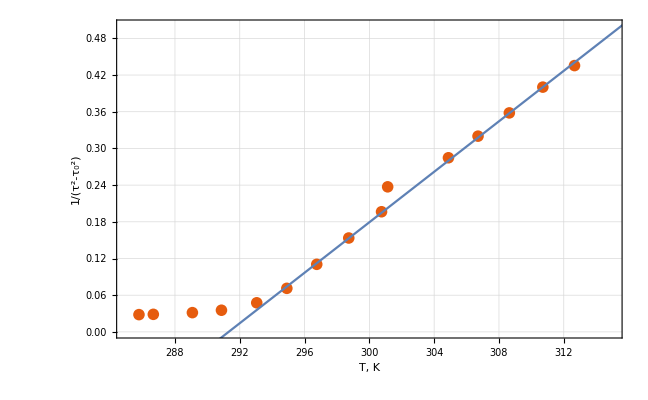

```mathematica
f1[τ_,τ0_]=-(2 τ)/((τ^2-τ0^2)^2);
f2[τ_,τ0_]=(2 τ0)/((τ^2-τ0^2)^2);
Errors = Table[0,{a,1,16}];
For[i=2, i≤16, i++,
Errors[[i]]=ErrorBar[√((f1[Experiment[[2,3]],9.050]*0.001)^2+(f2[Experiment[[2,3]],9.050]*0.001)^2)];
]
PlotData = Partition[Riffle[CalculatedData,Errors],2];
Delete[PlotData,{1}];
PlotPart = Take[CalculatedData,{7,16}];
PlotPart=Delete[PlotPart,{5}];
ApproximatedLine = LinearModelFit[PlotPart,x,x];
Normal[ApproximatedLine];
Show[ErrorListPlot[PlotData, PlotRange->{{285,315},{0,0.5}},PlotTheme->"Scientific", GridLines->Automatic],Plot[ApproximatedLine[x],{x,290,320}],FrameLabel->{{HoldForm[1/((Global`τ)^2-Subscript[Global`τ, 0]^2)],None},{RawBoxes[RowBox[{"T",","," ","K"}]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

Определим параметры графика, воспользовавшись методом наименьших квадратов:

```mathematica
ApproximatedLine["BestFit"]
```

-6.01127+0.0206351 x

```mathematica
ApproximatedLine["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -6.01127 | 0.0532307 | -112.929 | 1.12566×10^-12
x | 0.0206351 | 0.000175148 | 117.815 | 8.3691×10^-13

Рассчитаем значение Θ_p и σ_Θ_p:
Θ_p=-b/a=18.3 °С

σ_Θ= 0.01

Θ_p=(18.3±0.2)°С
 Вывод: исследовали поведение гадолиния при температуре выше температуры Кюри, убедились в выполнении для ферромагнитных веществ закона Кюри - Вейсса. Экспериментально для гадолиния вычислили точку Кюри Θ_p=(18.3±0.2)°С, что близко к табличному значению Θ_p=16 °С.